```mathematica
SetOptions[ListPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->24},Frame->True];
mup[k_]=Sqrt[(k+1)*(Np-k)];
mdown[k_]=Sqrt[k*(Np-k+1)];
mz[k_]=(2*k-Np);
eqn[k1_,k2_,k1p_,k2p_]=p[k1,k2,k1p,k2p]'[t]==-I*(mdown[k1]*mdown[k2]*p[k1-1,k2-1,k1p,k2p][t]+mdown[k1]*mup[k2]*p[k1-1,k2+1,k1p,k2p][t]+mup[k1]*mdown[k2]*p[k1+1,k2-1,k1p,k2p][t]+mup[k1]*mup[k2]*p[k1+1,k2+1,k1p,k2p][t])+I*(mdown[k1p]*mdown[k2p]*p[k1,k2,k1p-1,k2p-1][t]+mdown[k1p]*mup[k2p]*p[k1,k2,k1p-1,k2p+1][t]+mup[k1p]*mdown[k2p]*p[k1,k2,k1p+1,k2p-1][t]+mup[k1p]*mup[k2p]*p[k1,k2,k1p+1,k2p+1][t])-Γ*p[k1,k2,k1p,k2p][t]*((mz[k1]-mz[k1p])^2+(mz[k2]-mz[k2p])^2);
Szav1[t_]=Sum[(2*k1-Np)*psol[k1,k2,k1,k2][t],{k1,0,Np},{k2,0,Np}];
pinitial[k1_,k2_,k1p_,k2p_]=If[(k1==Np)&&(k2==Np)&&(k1p==Np)&&(k2p==Np),1.0,0.0];
idealcase[t_]=Cos[2*t]^Np;
partialtranspose[t_]:=ArrayFlatten[Table[psol[k1,k2p,k1p,k2][t],{k1,0,Np},{k1p,0,Np},{k2,0,Np},{k2p,0,Np}]];
negativity[t_]:=(Total[Abs[Eigenvalues[partialtranspose[t]]]]-1)/2;
lognegativitynorm[t_]:=Log[Np+1,Total[Abs[Eigenvalues[partialtranspose[t]]]]];
lognegativity[t_]:=Log[2,Total[Abs[Eigenvalues[partialtranspose[t]]]]];
timelist={1/Sqrt[2*Np]};
```

1

Γ=0.01 timelist index ii=1 icount=1

{1,0.971125}

{2,1.46456}

{3,1.76022}

{4,1.93294}

{5,2.045}

{6,2.17861}

{7,2.24208}

{8,2.33038}

{9,2.38913}

{10,2.42141}

{11,2.48368}

{12,2.50587}

{13,2.52781}

{14,2.56855}

{15,2.58313}

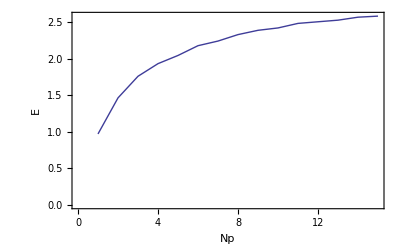

{{{1,0.971125},{2,1.46456},{3,1.76022},{4,1.93294},{5,2.045},{6,2.17861},{7,2.24208},{8,2.33038},{9,2.38913},{10,2.42141},{11,2.48368},{12,2.50587},{13,2.52781},{14,2.56855},{15,2.58313}}}

```mathematica
Γlist={0.01};Npmax=15;Npmin=1
Elistall={};
icount=0;
For[ii=1,ii<=Length[timelist],ii=ii+1,
For[jj=1,jj≤Length[Γlist],jj=jj+1,
Γ=Γlist[[jj]];
icount=icount+1;
Print["Γ=",Γ," timelist index ii=",ii," icount=",icount];
Elist={};
Elistnorm={};
For[Np=Npmin,Np≤Npmax,Np=Np+1,
tmax=timelist[[ii]];
vars={};
equations={};
For[k1=0,k1≤Np,k1=k1+1,
For[k2=0,k2≤Np,k2=k2+1,
For[k1p=0,k1p≤Np,k1p=k1p+1,
For[k2p=0,k2p≤Np,k2p=k2p+1,
equations=Append[equations,eqn[k1,k2,k1p,k2p]];
];
];
];
];
For[k1=0,k1≤Np,k1=k1+1,
For[k2=0,k2≤Np,k2=k2+1,
For[k1p=0,k1p≤Np,k1p=k1p+1,
For[k2p=0,k2p≤Np,k2p=k2p+1,
equations=Append[equations,p[k1,k2,k1p,k2p][0]==pinitial[k1,k2,k1p,k2p]];
vars=Append[vars,p[k1,k2,k1p,k2p]];
];
];
];
];
solutions=NDSolve[equations,vars,{t,0,tmax}];
Clear[k1,k2,k1p,k2p];
psol[k1_,k2_,k1p_,k2p_]:=p[k1,k2,k1p,k2p]/.solutions[[1]][[k1*(Np+1)^3+k2*(Np+1)^2+k1p*(Np+1)+k2p+1]];
Elist=Append[Elist,{Np,lognegativity[tmax]}];
Print[{Np,lognegativity[tmax]}];
];
p1=ListPlot[Elist,Joined->True,FrameLabel->{"Np","E"}];
Print[p1];
Elistall=Append[Elistall,Elist];
];
];
Print[Elistall];
```

```mathematica
Elistall={{{1,0.812318944225899},{2,1.2183232592017141},{3,1.4292989243827452},{4,1.5264012928765087},{5,1.5603776487199652},{6,1.570457459125377},{7,1.5689748506951966},{8,1.5606831590213064},{9,1.546381986820305},{10,1.52943982726752},{11,1.5127722054788113},{12,1.4948133269570414},{13,1.477061728488975},{14,1.4618018359013616},{15,1.4461813527410472}},{{1,0.8033004021098387},{2,1.1806159455445837},{3,1.3342641170089793},{4,1.4187604522385142},{5,1.4729202771026129},{6,1.5109532360029951},{7,1.5393739645541877},{8,1.5615866457290664},{9,1.5795379975718349},{10,1.5944217684065143},{11,1.607012202992719},{12,1.6178350545243891},{13,1.6272611879299013},{14,1.635560708390716},{15,1.642935572076365}},{{1,0.8033004021098387},{2,0.7134692977451087},{3,0.6545282187507518},{4,0.4182281246141381},{5,0.36596830589574764},{6,0.2570293311330667},{7,0.19477558143326654},{8,0.14137811329465957},{9,0.10851192210841108},{10,0.07603680974022264},{11,0.0641770559686007},{12,0.051990141634166556},{13,0.04234928128841064},{14,0.039061666256603296},{15,0.031971566194403146}}};
```

```mathematica
Elistnormall=Table[Table[{Elistall[[ii]][[jj]][[1]],Elistall[[ii]][[jj]][[2]]/Log[2,Elistall[[ii]][[jj]][[1]]+1]},{jj,1,Length[Elistall[[ii]]]}],{ii,1,Length[Elistall]}]
```

{{{1,0.812319},{2,0.768676},{3,0.714649},{4,0.657385},{5,0.603636},{6,0.559408},{7,0.522992},{8,0.492341},{9,0.465507},{10,0.442107},{11,0.421977},{12,0.403956},{13,0.38795},{14,0.37416},{15,0.361545}},{{1,0.8033},{2,0.744886},{3,0.667132},{4,0.611027},{5,0.569803},{6,0.538212},{7,0.513125},{8,0.492626},{9,0.475488},{10,0.460891},{11,0.448265},{12,0.437201},{13,0.427399},{14,0.418635},{15,0.410734}},{{1,0.8033},{2,0.450149},{3,0.327264},{4,0.180121},{5,0.141576},{6,0.0915557},{7,0.0649252},{8,0.0445998},{9,0.0326653},{10,0.0219796},{11,0.0179017},{12,0.0140497},{13,0.011123},{14,0.00999815},{15,0.00799289}}}

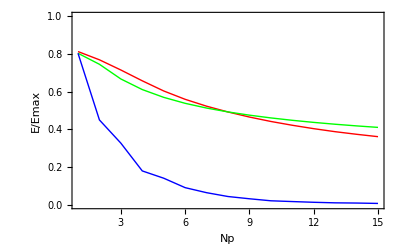

```mathematica
p3=ListPlot[{Elistnormall[[1]],Elistnormall[[2]],Elistnormall[[3]]},FrameLabel->{"Np","E/Emax"},PlotRange->{0,1},Joined->True,PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1]}];
Print[p3];
```

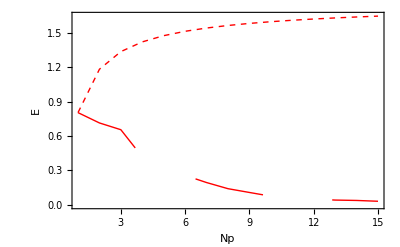

```mathematica
ppis=ListPlot[{Elistall[[2]],Elistall[[3]]},Joined->True,FrameLabel->{"Np","E"},PlotRange->{0,Automatic},PlotStyle->{{RGBColor[1,0,0],Dashing[0.01]},{RGBColor[1,0,0],Dashing[10]},{RGBColor[0,0,1],Dashing[0.01]},{RGBColor[0,0,1],Dashing[10]}}];
Print[ppis];
```